```mathematica
(*3.1a*)
(*Calculate the radius Subscript[r, 0]​and the period T of the limit cycle for μ>0*)
```

```mathematica
f[r_]=μ*r-r^3;
g[r_]=ω+ν*r^2;
fixedP=Solve[{f[r,θ]==0},r]
```

{{r→0},{r→-√μ},{r→√μ}}

```mathematica
(*We only want to evaluate r>0(radius is a length)l, therefore the only relevant fixed point is the third which is the radius of the cycle*)
fp = fixedP[[3]]
```

{r→√μ}

```mathematica
Subscript[r, 0]=fp[[1]][[2]]
```

√μ

```mathematica
T = 2π/g[r,θ]/.fp
```

(2 π)/(μ ν+ω)

```mathematica
(*3.2b*)
(*(b) Make a phase portrait of the dynamical system (2) showing a few representative trajectories.In the same figure,plot the limit cycle using a suitable representative trajectory.*)
```

```mathematica
(* I begin to solve 3.2c to find the values of μ, ω and ν*)
(* 3.2c *)
(* Convert system 1 to cartesian*)
X1Dot[x,y]=f[r]*Cos[θ]-r*g[r]*Sin[θ] /.{r->Sqrt[Subscript[X, 1]^2+Subscript[X, 2]^2],θ->ArcTan[Subscript[X, 1],Subscript[X, 2]]} // ExpandAll
X2Dot[x,y]=f[r]*Cos[θ]+r*g[r]*Sin[θ] /.{r->Sqrt[Subscript[X, 1]^2+Subscript[X, 2]^2],θ->ArcTan[Subscript[X, 1],Subscript[X, 2]]} // 
ExpandAll
```

μ X_1-X_1^3-ω X_2-ν X_1^2 X_2-X_1 X_2^2-ν X_2^3

μ X_1-X_1^3+ω X_2+ν X_1^2 X_2-X_1 X_2^2+ν X_2^3

```mathematica
(* We can compare the output with system 2;*)
(* Streamplot system 2 *)
Subscript[X1Dot, 2]= 1/10*Subscript[X, 1][t]-(Subscript[X, 2][t])^3-Subscript[X, 1][t]*(Subscript[X, 2][t])^2-(Subscript[X, 1][t])^2*Subscript[X, 2][t]-Subscript[X, 2][t]-(Subscript[X, 1][t])^3;
Subscript[X2Dot, 2]=Subscript[X, 1][t]+1/10*Subscript[X, 2][t]+Subscript[X, 1][t]*(Subscript[X, 2][t])^2+(Subscript[X, 1][t])^3-(Subscript[X, 2][t])^3-(Subscript[X, 1][t])^2*Subscript[X, 2][t];
(*From comparison we get values *)
μ=1/10;
ω=1;
ν=1;
```

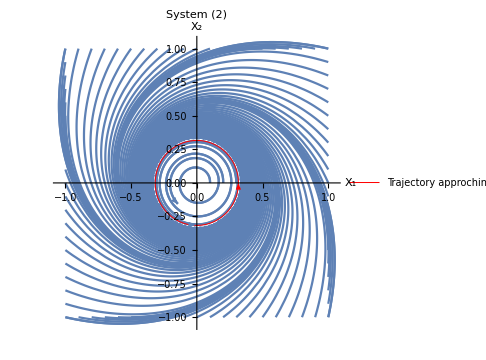

```mathematica
(*Circle plot*)
circle = ParametricPlot[{Subscript[r, 0]*Cos[t], Subscript[r, 0]*Sin[t]}, {t, 0, 2π}, PlotStyle->{Thickness[0.002], Red},PlotLegends->{"Trajectory approching a limit cycle"}]/.Line[x_]:> Sequence[Arrowheads[{0.015,0.015,0.015,0.015,0.015}],Arrow[x]];
(*Outer plot*)
sol1[X10_, X20_]:=NDSolve[{Subscript[X, 1]'[t]==Subscript[X1Dot, 2], Subscript[X, 2]'[t]==Subscript[X2Dot, 2], Subscript[X, 1][0]== X10, Subscript[X, 2][0]==X20}, {Subscript[X, 1], Subscript[X, 2]}, {t, 10}];
inits = Join[Table[{-1, Subscript[X, 2]}, {Subscript[X, 2], -1, 1, 0.1}],Table[{1, Subscript[X, 2]}, {Subscript[X, 2], -1, 1, 0.1}],Table[{Subscript[X, 1], -1},{Subscript[X, 1], -1, 1, 0.1}],Table[{Subscript[X, 1], 1},{Subscript[X, 1], -1, 1, 0.1}]];

outer = Table[ParametricPlot[Evaluate[{Subscript[X, 1][t], Subscript[X, 2][t]}/.sol1[inits[[i, 1]], inits[[i, 2]]]], {t, 0, 10}, PlotRange->All]/.Line[x_]:> Sequence[Arrowheads[{0.015,0.015,0.015,0.015,0.015}],Arrow[x]], {i, Length[inits]}];

(* Plot the inner part *)
sol2[X10_, X20_]:=NDSolve[{Subscript[X, 1]'[t]==Subscript[X1Dot, 2], Subscript[X, 2]'[t]==Subscript[X2Dot, 2], Subscript[X, 1][0]== X10, Subscript[X, 2][0]==X20}, {Subscript[X, 1], Subscript[X, 2]}, {t, 10}];
inits = Join[Table[{0, Subscript[X, 2]}, {Subscript[X, 2], 0, 0, 0.1}],Table[{0, Subscript[X, 2]}, {Subscript[X, 2], 0, 0, 0.1}],Table[{Subscript[X, 1], 0},{Subscript[X, 1], 0, Subscript[r, 0], 0.1}],Table[{Subscript[X, 1], 0},{Subscript[X, 1], 0, Subscript[r, 0], 0.1}]];
inner= Table[ParametricPlot[Evaluate[{Subscript[X, 1][t], Subscript[X, 2][t]}/.sol2[inits[[i, 1]], inits[[i, 2]]]], {t, 0, 10}, PlotRange->All]/.Line[x_]:> Sequence[Arrowheads[{0.02,0.02,0.02,0.02}],Arrow[x]], {i, Length[inits]}];
p4=Show[outer, inner, circle, PlotLabel->"System (2)", AxesLabel->{Subscript[X, 1],Subscript[X, 2]}, ImageSize->Medium]
(*Export["3.2b.jpg",p4]*)
```

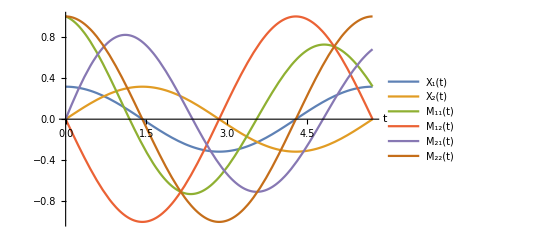

```mathematica
(*3.2d*)
(*Plot all six quantities as functions of tt for one period TT of the limit cycle*)
(*We only consider system 2*)
J=Grad[{Subscript[X1Dot, 2], Subscript[X2Dot, 2]}, {Subscript[X, 1][t], Subscript[X, 2][t]}];
sol3 =NDSolve[{Subscript[X, 1]'[t]==Subscript[X1Dot, 2],Subscript[X, 2]'[t]==Subscript[X2Dot, 2],Subscript[M, 11]'[t]==J[[1]][[1]]*Subscript[M, 11][t]+J[[1]][[2]]*Subscript[M, 21][t],Subscript[M, 12]'[t]==J[[1]][[1]]*Subscript[M, 12][t]+J[[1]][[2]]*Subscript[M, 22][t],Subscript[M, 21]'[t]==J[[2]][[1]]* Subscript[M, 11][t]+J[[2]][[2]]*Subscript[M, 21][t],Subscript[M, 22]'[t]==J[[2]][[1]]*Subscript[M, 12][t]+J[[2]][[2]]*Subscript[M, 22][t],Subscript[X, 1][0]==Sqrt[μ],Subscript[X, 2][0]==0,Subscript[M, 11][0]==1,Subscript[M, 12][0]==0,Subscript[M, 21][0]==0,Subscript[M, 22][0]==1},{Subscript[X, 1][t],Subscript[X, 2][t],Subscript[M, 11][t],Subscript[M, 12][t],Subscript[M, 21][t],Subscript[M, 22][t]},{t,0,T}];

(* Plot with different colors for each line *)
p5=Plot[Evaluate[{Subscript[X, 1][t],Subscript[X, 2][t],Subscript[M, 11][t],Subscript[M, 12][t],Subscript[M, 21][t],Subscript[M, 22][t]}/.sol3],{t, 0, T}, PlotStyle->Automatic,PlotLegends->{Subscript[X, 1][t],Subscript[X, 2][t],Subscript[M, 11][t],Subscript[M, 12][t],Subscript[M, 21][t],Subscript[M, 22][t]},AxesLabel->{Style[t,FontSize->18],""}]
(*Export["3.2d_plot.jpg", p5]*)
```

```mathematica
(*3.2e*)
(*Give your numerical M(T) obtained in (d) to 4 relevant digits accuracy*)
```

```mathematica
M2[t_]={{Subscript[M, 11][t],Subscript[M, 12][t]},{Subscript[M, 21][t],Subscript[M, 22][t]}}/. sol3;
(*two different ways to use for numerical solutions*)
N[Floor[M2[T]*10000],4]/10000
NumberForm[M2[T],4,ExponentFunction->(Null&)]
```

{{{0.319,0},{0.6809,1.}}}

{{{0.3191,0.00000002123},{0.6809,1.}}}

```mathematica
(*With 4 decimals the numerical result is [0.3191,0],[0.6809,1]*)
```

```mathematica
(*3.2f*)
(*alculate the stability exponents of separations (​σ)_1 and Subscript[σ, 2] of the limit cycle from the eigenvalues of M(T) to 4 relevant digits accuracy*)
```

```mathematica
eigV1 = Eigenvalues[M[T]];
σ=N[Floor[1/T*Log[eigV1]*10000]/10000]
```

{0.,-0.2}

```mathematica
(*So Subscript[σ, 1] is -0.2 and Subscript[σ, 2] is 0 because Subscript[σ, h1] ≤ Subscript[σ, h2] *)
(*3.2g*)
(*Using what you know from all parts of this problem,calculate the deformation matrix M(T) analytically.*)
```

```mathematica
jacobian=Grad[{f[r],g[r]},{r,θ}];
J2=jacobian/.r->Subscript[r, 0];
M3=MatrixExp[T*J2] //FullSimplify;
(* Write in cartesian coord. by multiplying left and right *)
J3 =Grad[{Sqrt[x[t]^2+y[t]^2],ArcTan[x[t],y[t]]},{x[t],y[t]}] /. t->T/.{x[T]->Subscript[r, 0]*Cos[0],y[T]->Subscript[r, 0]*Sin[0]};
Subscript[M, cartesian]=Inverse[J3].M3.J3
```

{{ⅇ^(-4 π/11),0},{1-ⅇ^(-4 π/11),1}}

```mathematica
(*3.2h*)
(*Compute the stability exponents of separations (​σ)_1 and (​σ)_2 of the limit cycle analytically*)
eigV2 = Eigenvalues[Subscript[M, cartesian]];
Subscript[σ, h]=1/T*Log[eigV2]
```

{0,-1/5}

```mathematica
(*So Subscript[σ, 1] is -1/5 and Subscript[σ, 2] is 0 because Subscript[σ, h1] ≤ Subscript[σ, h2] *)
```